```mathematica
Quantity[Around[31.4,{31.1,31.6}],"Percent"]
```

(31.31.32.) %

```mathematica
Clear[pct];
pct /: pct[avg_?NumericQ, max_?NumericQ, min_?NumericQ] := Quantity[Around[avg,{Abs[avg-min],Abs[max-avg]}], "Percent"]
```

```mathematica
years=Reverse@(DateObject[#,"Year"]&/@DateRange[{2011},{2020},"Year"]);
```

```mathematica
Clear[obesity];
obesity["USAAverage"]=pct@@@{
{31.9,31.6,32.3},
{31.4,31.1,31.6},
{30.9,30.6,31.2},
{30.1,29.8,30.4},
{29.6,29.3,29.8},
{28.9,28.6,29.1},
{28.9,28.6,29.2},
{28.3,28.0,28.6},
{27.7,27.4,28.0},
{27.4,27.2,27.7}
};
obesity["MO"] = pct @@@ {
{34.0,32.7,35.4},
{34.8,33.2,36.4},
{35.0,33.3,36.8},
{32.5,30.9,34.0},
{30.2,28.6,31.9},
{30.4,28.8,32.1},
{29.6, 28.0,31.2},
{30.3,28.6,32.0},
{32.4,30.8,34.0},
{31.7,30.0,33.4}
};
```

```mathematica
Clear[overweight];
overweight["USAAverage"] = pct@@@{
{35.8,35.5,36.1},
{35.7,35.4,36.0},
{35.5,35.2,35.8},
{35.2,34.9,35.5},
{35.7,35.4,36.0},
{35.2,34.9,35.5},
{35.3,35.0,35.6},
{35.0,34.7,35.3},
{35.2,34.9,35.6},
{34.8,34.5,35.2}
};
overweight["MO"] = pct@@@{
{34.6,32.9,36.3},
{36.2,34.5,37.9},
{35.1,33.4,36.8},
{35.4,33.7,37.1},
{33.9,32.3,35.5},
{35.6,33.8,37.4},
{35.4,33.8,37.0},
{31.9,30.2,33.6},
{33.3,31.7,34.9},
{35.4,34.1,36.8}
};
```

```mathematica
Clear[ts];
ts["Obesity","USAAverage"]=TimeSeries[Partition[Riffle[years, obesity["USAAverage"]],2]]
ts["Obesity","MO"] = TimeSeries[Partition[Riffle[years, obesity["MO"]], 2]]
ts["Overweight","USAAverage"]=TimeSeries[Partition[Riffle[years,overweight["USAAverage"]],2]]
ts["Overweight", "MO"]=TimeSeries[Partition[Riffle[years, overweight["MO"]],2]]
```

TimeSeries[…]

TimeSeries[…]

TimeSeries[…]

«1 more identical outputs»

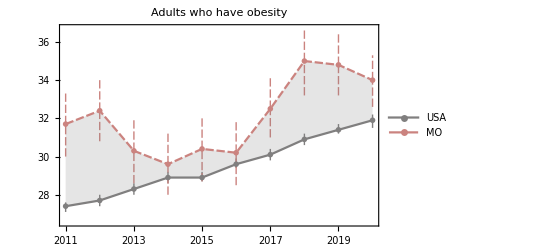

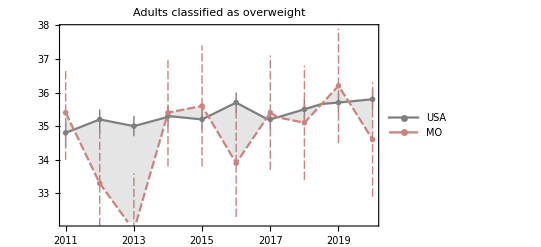

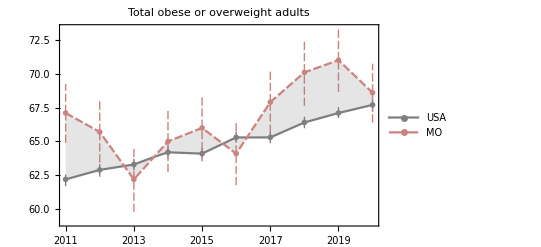

```mathematica
DateListPlot[{ts["Obesity","USAAverage"], ts["Obesity","MO"]},PlotLabel->"Adults who have obesity",
PlotLegends->{"USA","MO"},
PlotTheme->"Monochrome",
PlotStyle->7,
FrameLabel->Automatic,
Filling -> {1 -> {2}}
]
DateListPlot[{ts["Overweight","USAAverage"], ts["Overweight", "MO"]}, PlotLabel->"Adults classified as overweight",
 PlotLegends->{"USA","MO"},
PlotTheme->"Monochrome",
PlotStyle->7,
FrameLabel->Automatic,
Filling -> {1 -> {2}}
]
DateListPlot[{
ts["Overweight","USAAverage"]+ts["Obesity","USAAverage"],
ts["Overweight","MO"]+ts["Obesity","MO"]
},
PlotLabel->"Total obese or overweight adults",
PlotLegends->{"USA","MO"},
PlotTheme -> "Monochrome", 
PlotStyle->7,
FrameLabel->Automatic,
Filling -> {1 -> {2}}
]
```